Bretcher 1.2.2

```mathematica
Solve[3x+4y-z==8&&6x+8y-2z==3,{x,y,z}]
```

{}

Empty brackets in mathematica means that there is no solutions to the systems.

```mathematica
ContourPlot3D[{3x+4y-z==8,6x+8y-2z==3},{x,-8,8},{y,-8,8},{z,-8,8}]
```

-Graphics3D-

On the plot above we also see that the planes are parallel and therefore no solutions.

Bretcher 1.2.32

We want to find a polynomial of degree 3 which is expressed as p(x)=a+bx+cx^2+dx^3.
By setting in the given points we get a system of equation

```mathematica
Solve[{a==1,a+b+c+d==0,a-b+c-d==0,a+2b+4c+8d==15},{a,b,c,d}]
```

Solve::ivar: {{8},{1},{-2},{-15}} is not a valid variable.

Solve[{a==1,{{8+a+c+d},{1+a+c+d},{-2+a+c+d},{-15+a+c+d}}==0,{{-8+a+c-d},{-1+a+c-d},{2+a+c-d},{15+a+c-d}}==0,{{16+a+4 c+8 d},{2+a+4 c+8 d},{-4+a+4 c+8 d},{-30+a+4 c+8 d}}==15},{a,{{8},{1},{-2},{-15}},c,d}]

The equations is converted into matrix form and solved accordingly.

```mathematica
MatrixForm[m={{1, 0, 0, 0, 1}, {1, 1, 1, 1, 0}, {1, -1, 1, -1, 0}, {1, 2, 4, 8, 15}}];
```

```mathematica
RowReduce[m] //MatrixForm
```

(1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | -3
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | 3)

We plot the polynomial with  the coefficients that were calculated in stage 1 and get the answer:

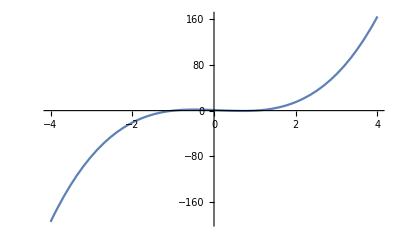

```mathematica
Plot[1-3t-t^2+3t^3, {t,-4,4}]
```